```mathematica
<<SpaceMath`
```

SpaceMath v.1.0 | 
Documentation Centerpaclet:SpaceMath/tutorial/SpaceMathOverview | 
 | Examples
Cite |  | -Graphics-
Authors:
  ⊕ M. A. Arroyo-Ureña
 Facultad de Estudios Superiores-Cuautitlán, Universidad Nacional Autónoma de México
  ⊗ T. A. Valencia-Pérez
 Instituto de Física, Universidad Nacional Autónoma de México
 Contact us:	spacemathapp@gmail.com |

```mathematica
ghtt[cα_,Ztt_,u_]:= ((cα*mt)/ vev)-((Sqrt[1-cα^2] Ztt vev)/(Sqrt[2] u))
ghbb[cα_,Zbb_,u_]:= ((cα*mb)/ vev)-((Sqrt[1-cα^2] Zbb vev)/(Sqrt[2] u))
ghtautau[cα_,Ztautau_,u_]:= ((cα*mtau)/ vev)-((Sqrt[1-cα^2] Ztautau vev)/(Sqrt[2] u))
ghmumu[cα_,Zmumu_,u_]:= ((cα*mmu)/ vev)-((Sqrt[1-cα^2] Zmumu vev)/(Sqrt[2] u))
ghWW[cα_]:= gw*mW*cα
ghZZ[cα_]:= gz*mZ*cα
ghtaumu[cα_,Ztaumu_,u_]:= -((Sqrt[1-cα^2] Ztaumu vev)/(Sqrt[2] u))
gHmumu[cα_,Zmumu_,u_]:= ((√(1-cα^2)*mmu)/ vev)+(cα Zmumu vev)/(Sqrt[2] u)
gHtaumu[cα_,Ztaumu_,u_]:= (cα Ztaumu vev)/(Sqrt[2] u)
gAmumu[Zmumu_,u_]:= I*Zmumu /(Sqrt[2] u)
gAtaumu[Ztaumu_,u_]:= I*Ztaumu /(Sqrt[2] u)
gHmue[cα_,Zmue_,u_]:= (cα Zmue vev)/(Sqrt[2] u)
ghmue[cα_,Zmue_,u_]:= -((Sqrt[1-cα^2] Zmue vev)/(Sqrt[2] u))
gAmue[Zmue_,u_]:= I*Zmue /(Sqrt[2] u)
gHee[cα_,Zee_,u_]:= ((√(1-cα^2)*me)/ vev)+(cα Zee vev)/(Sqrt[2] u)
gAee[Zee_,u_]:= I*Zee /(Sqrt[2] u)
ghee[cα_,Zee_,u_]:= ((cα*me)/ vev)-((Sqrt[1-cα^2] Zee vev)/(Sqrt[2] u))
```

```mathematica
Tau3Mu[ghmumu[ca,0.001,u],ghtaumu[ca,0.001,u],gHmumu[ca,0.001,u],gHtaumu[ca,Ztaumu,u],gAmumu[0.001,u],gAtaumu[Ztaumu,u],mH,500, ca, -1, 1,u, 10,2000, Ztaumu,0.1,0.4,mH, 200,1000,5000]
```

{Null}

```mathematica
Zee=0.0001;
```

```mathematica
Mu3e[ghmue[ca,Zee,u],ghmue[ca,Zmue,u],gHmue[ca,Zee,u],gHmue[ca,Zmue,u],gAmue[Zee,u],gAmue[Zmue,u],mH,500, ca, -1, 1,u, 10,2000, Zmue,0,0.1,mH, 200,1000,5000]
```

{Null}

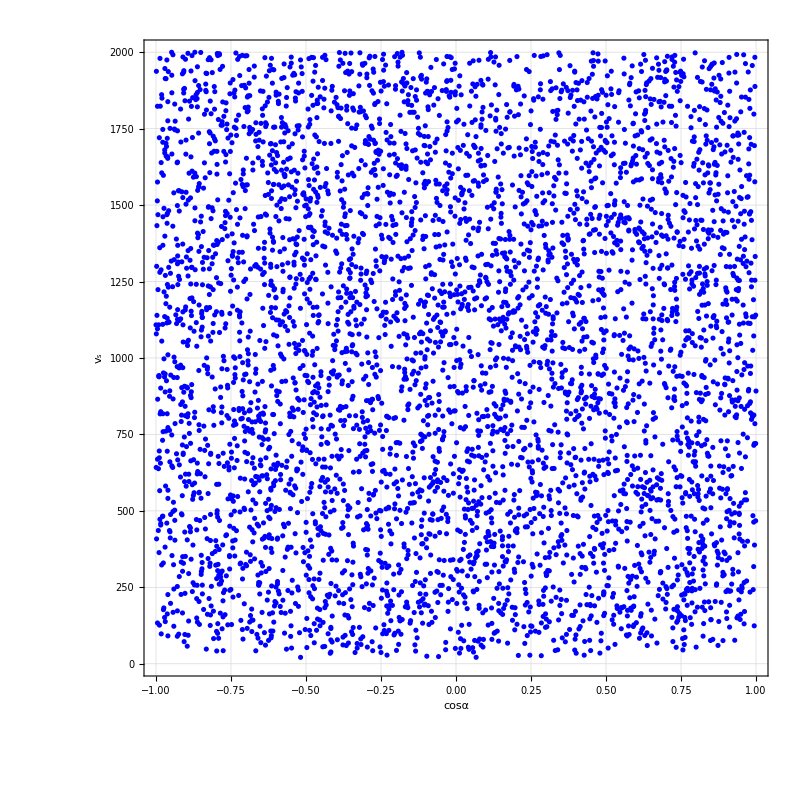

```mathematica
PlotTau3Mu[1, 2, "cosα", "v_s"]
```

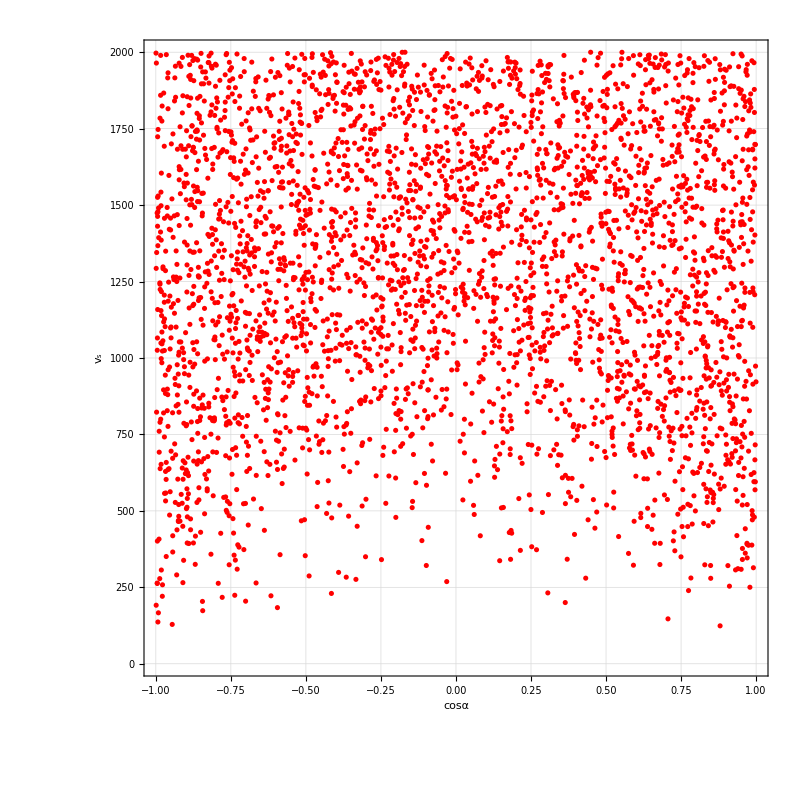

```mathematica
PlotMu3e[1, 2, "cosα", "v_s"]
```

```mathematica
BRmuto3electrons[ghmue[ca,Zee,u],ghmue[ca,Zmue,u],gHmue[ca,Zee,u],gHmue[ca,Zmue,u],gAmue[Zee,u],gAmue[Zmue,u],500,500]
```

7.30187×10^-15+0. ⅈ

```mathematica
me
```

0.000510999

```mathematica
BRTAUtoEEE//N
```

2.7×10^-8

```mathematica
muonAMDM[ghmumu[ca,0.001,u], ghtaumu[ca,0.001,u],gHmumu[ca,0.001,u],gHtaumu[ca,Ztaumu,u],gAmumu[0.001,u],gAtaumu[Ztaumu,u],mH,500, ca,-1, 1,
u, 10, 2000, Ztaumu, 0.1, 0.4, mH, 200, 1000, 500]
```

```mathematica
PlotMuonAMDM[1, 2, "cosα", "v_s"]
```